## Zad 1.

```mathematica
a= Random[Integer,{0,20}]
b= Random[Real, {-100, 100}]
PrimeQ[a]
b>0
```

18

72.4044

False

True

## Zad 2.

=        -  przypisywanie zmiennej, wartości funkcji itp. do zmiennej,
==      - porównywanie ze sobą np. wyników operacji matematycznej, wartości zmiennych itp.
===    - tożsamość, porównywanie czy dwa obiekty wskazują na to samo miejsce w pamięci

## Zad 3.

```mathematica
Fibo[n_]:=Fibo[n]=Fibo[n-1]+Fibo[n-2];
Fibo[1]=1;Fibo[2]=1;
FiboArr = Array[Fibo, 10]

f[n_]:=f[n-1]^2;
f[1]=3;
Array[f, 5]
```

{1,1,2,3,5,8,13,21,34,55}

{3,9,81,6561,43046721}

## Zad 4.

=       - wartość funkcji jest obliczana przy de definiowaniu funkcji
= :    - wartość funkcji jest obliczana przy wywołaniu funkcji dla argumentu

## Zad 5.

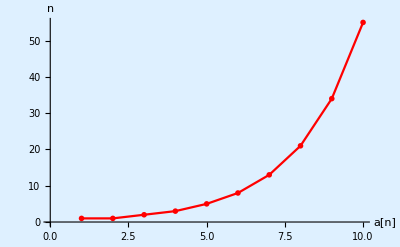

```mathematica
ListPlot[FiboArr, AxesLabel->{"a[n]", "n"}, Background->LightBlue, PlotStyle->Red, PlotMarkers-> "OpenMarkers", Joined->True]
```

## Zad 6.

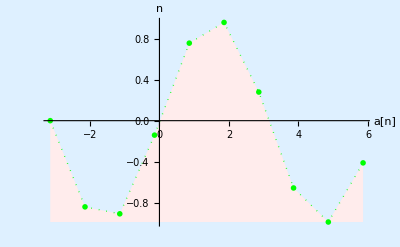

```mathematica
ListPlot[Table[{x, Sin[x]}, {x,-Pi, 2*Pi}], AxesLabel->{"a[n]", "n"}, Background->LightBlue, PlotStyle->{Thick, Green, Dotted}, PlotMarkers->"OpenMarkers", Joined->True, Filling->Bottom, FillingStyle->LightPink]
```

## Zad 7.

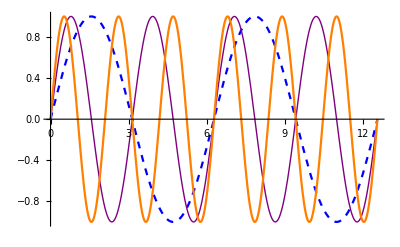

```mathematica
f1 = Plot[Sin[x], {x,0, 4*Pi},  PlotStyle->{Blue, Dashed}];
f2 = Plot[Sin[2*x], {x,0, 4*Pi},  PlotStyle->{Purple, Thick}];
f3=Plot[Sin[3*x], {x,0, 4*Pi},  PlotStyle->{Orange}];
Show[f1,f2,f3]
```

## Zad 8.

```mathematica
Plot3D[Sin[x^2+y^2],{x,-Pi,Pi},{y,-Pi,Pi},PlotStyle->{Green},Axes->False,Mesh->None,AspectRatio->Automatic]
```

-Graphics3D-

## Zad 9.

```mathematica
ParametricPlot3D[{Cos[t]*(3+Cos[u]),Sin[t]*(3+Cos[u]),Sin[u]},{t,0,2*Pi},{u,0,2*Pi},PlotStyle->LightRed,AspectRatio->Automatic]
```

-Graphics3D-

## Zad 10.

```mathematica
Animate[Plot[E^(Sin[t*x]),{x,-π,π},PlotRange->{0,3}],{t,0,4},AnimationRunning->False]
```

```mathematica
Animate[Plot[E^(Sin[t*x]),{x,-π,π},PlotRange->{0,3}],{t,0,8,2},AnimationRunning->False]
```

```mathematica
Animate[Plot[E^(Sin[t*x]),{x,-π,π},PlotRange->{0,3}],{t,{0,4,7,8}},AnimationRunning->False]
```

## Zad 11.

```mathematica
Animate[Plot3D[E^(a*Sin[x+y]+b*Cos[x-y]),{x,0,2*π},{y,0,2*π},PlotRange->{0,9}],{a,0,1},{b,0,9,2},AnimationRunning->False]
```

## Zad 12.

```mathematica
Animate[Plot[Factorial[x],{x,0,n}],{n,1,10,1},AnimationRunning->False]
```